## Initial

```mathematica
ClearAll["Global`*"]
NotebookDirectory[]
SetDirectory["/Users/wange/Documents/Research/spin/wien/"];
```

/Users/wange/Documents/Research/spin/wien/

## Wien track

```mathematica
(* ================================================================*)(*Relativistic electron tracking through a Wien filter*)(*Phase space:{x,y,z,px,py,pz} in SI units*)(*E table:{{z,Ex},...} with z in m and Ex in V/m*)(*B table:{{z,B},...} with z in m and B in T*)(*Default interpretation:E=Ex(z) xhat,B=B(z) yhat*)(* ================================================================*)ClearAll[WienFilterTrack,MomentumFromKineticEnergyEV,EVoverCToSI,SIToEVoverC];

(*----------Useful unit helpers----------*)

MomentumFromKineticEnergyEV[KEeV_,m_:9.1093837015*10^-31,c_:299792458.]:=Module[{e=1.602176634*10^-19,KJ},KJ=KEeV*e;
Sqrt[(KJ+m*c^2)^2-(m*c^2)^2]/c];

EVoverCToSI[pEVoverC_]:=pEVoverC*1.602176634*10^-19/299792458.;

SIToEVoverC[pSI_]:=pSI*299792458./1.602176634*10^-19;

ClearAll[RandomNormalOrFixed];

RandomNormalOrFixed[mean_,sigma_]:=If[sigma==0,mean,RandomVariate[NormalDistribution[mean,sigma]]];
(*----------Main tracker----------*)

Options[WienFilterTrack]={"Step"->0.01,(*output z step,m*)"ZStart"->Automatic,"ZEnd"->Automatic,"Charge"->-1.602176634*10^-19,(*electron charge,C*)"Mass"->9.1093837015*10^-31,(*electron rest mass,kg*)"SpeedOfLight"->299792458.,"EDirection"->{1.,0.,0.},(*default Ex*)"BDirection"->{0.,1.,0.},(*default By*)"InterpolationOrder"->3,(*linear interpolation for fringe fields*)AccuracyGoal->10,PrecisionGoal->10,MaxStepFraction->1/200,MaxSteps->Infinity,Method->Automatic};(*"InterpolationOrder"->1, dont use 0*)

WienFilterTrack[particlesIn_,eTableIn_,bTableIn_,OptionsPattern[]]:=Module[{particles,eTable,bTable,q,m,c,eAbs,step,zStart,zEnd,zPlanes,eDir,bDir,ord,makeFieldFunction,eAmp,bAmp,fieldE,fieldB,gamma,velocity,dpdzVec,dpdz1,dpdz2,dpdz3,ndOpts,trackOne,sols,sampleOne,fullSamples,distributions,timeOfFlight,kineticEnergyEV,rmsEmit,statsAtPlane,beamParameters},(*-----numerical input-----*)particles=N[particlesIn];
eTable=N[eTableIn];
bTable=N[bTableIn];
If[!MatrixQ[particles,NumericQ]||Dimensions[particles][[2]]=!=6,Print["Error: particles must be an N x 6 numerical array: {x,y,z,px,py,pz}."];
Return[$Failed];];
If[!MatrixQ[eTable,NumericQ]||Dimensions[eTable][[2]]=!=2,Print["Error: eTable must be a numerical array {{z, Ex}, ...}."];
Return[$Failed];];
If[!MatrixQ[bTable,NumericQ]||Dimensions[bTable][[2]]=!=2,Print["Error: bTable must be a numerical array {{z, B}, ...}."];
Return[$Failed];];
q=OptionValue["Charge"];
m=OptionValue["Mass"];
c=OptionValue["SpeedOfLight"];
eAbs=1.602176634*10^-19;
step=OptionValue["Step"];
ord=OptionValue["InterpolationOrder"];
If[step<=0,Print["Error: output step must be positive."];
Return[$Failed];];
eDir=N[OptionValue["EDirection"]];
bDir=N[OptionValue["BDirection"]];
eDir=eDir/Sqrt[eDir.eDir];
bDir=bDir/Sqrt[bDir.bDir];
zStart=OptionValue["ZStart"]/. Automatic->Max[particles[[All,3]]];
zEnd=OptionValue["ZEnd"]/. Automatic->Max[Join[eTable[[All,1]],bTable[[All,1]],particles[[All,3]]]];
If[zEnd<=zStart,Print["Error: ZEnd must be larger than ZStart for forward +z tracking."];
Return[$Failed];];
zPlanes=DeleteDuplicates[N@Join[Range[zStart,zEnd,step],{zEnd}],Abs[#1-#2]<10^-12&];
(*-----field interpolation;outside table range,field is set to zero-----*)makeFieldFunction[tab_]:=Module[{tt,zmin,zmax,int},tt=DeleteDuplicatesBy[SortBy[N[tab],First],First];
If[Length[tt]<2,Return[Function[{zz},0.]]];
{zmin,zmax}=MinMax[tt[[All,1]]];
int=Interpolation[tt,InterpolationOrder->ord];
Function[{zz},If[zmin<=zz<=zmax,int[zz],0.]]];
eAmp=makeFieldFunction[eTable];
bAmp=makeFieldFunction[bTable];
fieldE[z_?NumericQ]:=eAmp[z]*eDir;
fieldB[z_?NumericQ]:=bAmp[z]*bDir;
(*-----relativistic mechanics-----*)gamma[px_,py_,pz_]:=Sqrt[1.+(px^2+py^2+pz^2)/(m^2*c^2)];
velocity[px_?NumericQ,py_?NumericQ,pz_?NumericQ]:={px,py,pz}/(gamma[px,py,pz]*m);
(*Independent variable is z,not t.dx/dz=vx/vz=px/pz dy/dz=vy/vz=py/pz dp/dz=q (E+v x B)/vz*)dpdzVec[z_?NumericQ,px_?NumericQ,py_?NumericQ,pz_?NumericQ]:=Module[{v,vz},v=velocity[px,py,pz];
vz=v[[3]];
q*(fieldE[z]+Cross[v,fieldB[z]])/vz];
dpdz1[z_?NumericQ,px_?NumericQ,py_?NumericQ,pz_?NumericQ]:=dpdzVec[z,px,py,pz][[1]];
dpdz2[z_?NumericQ,px_?NumericQ,py_?NumericQ,pz_?NumericQ]:=dpdzVec[z,px,py,pz][[2]];
dpdz3[z_?NumericQ,px_?NumericQ,py_?NumericQ,pz_?NumericQ]:=dpdzVec[z,px,py,pz][[3]];
ndOpts={AccuracyGoal->OptionValue[AccuracyGoal],PrecisionGoal->OptionValue[PrecisionGoal],MaxStepFraction->OptionValue[MaxStepFraction],MaxSteps->OptionValue[MaxSteps],Method->OptionValue[Method]};
(*-----track one particle-----*)trackOne[p0_]:=Module[{x0,y0,z0,px0,py0,pz0,x,y,px,py,pz,t,s},{x0,y0,z0,px0,py0,pz0}=p0;
If[pz0<=0,Print["Warning: particle has non-positive initial pz. Tracking may fail."]];
NDSolveValue[{x'[s]==px[s]/pz[s],y'[s]==py[s]/pz[s],px'[s]==dpdz1[s,px[s],py[s],pz[s]],py'[s]==dpdz2[s,px[s],py[s],pz[s]],pz'[s]==dpdz3[s,px[s],py[s],pz[s]],t'[s]==gamma[px[s],py[s],pz[s]]*m/pz[s],x[z0]==x0,y[z0]==y0,px[z0]==px0,py[z0]==py0,pz[z0]==pz0,t[z0]==0.,WhenEvent[pz[s]<=0,"StopIntegration"]},{x,y,px,py,pz,t},{s,z0,zEnd},Evaluate[Sequence@@ndOpts]]];
sols=trackOne/@particles;
(*-----sample all particles at requested z planes-----*)sampleOne[sol_,zz_]:=Module[{dom,vals},dom=sol[[1]]["Domain"][[1]];
If[zz<dom[[1]]||zz>dom[[2]],Missing["NotTracked"],vals=Through[sol[zz]];
(*Return {x,y,z,px,py,pz,t}*){vals[[1]],vals[[2]],zz,vals[[3]],vals[[4]],vals[[5]],vals[[6]]}]];
fullSamples=Table[DeleteCases[sampleOne[#,zz]&/@sols,_Missing],{zz,zPlanes}];
distributions=fullSamples[[All,All,1;;6]];
timeOfFlight=fullSamples[[All,All,7]];
(*-----beam statistics-----*)kineticEnergyEV[pvec_]:=Module[{g},g=Sqrt[1.+(pvec.pvec)/(m^2*c^2)];
(g-1.)*m*c^2/eAbs];
rmsEmit[data_]:=If[Length[data]<2,0.,Sqrt[Max[0.,Det[Covariance[data]]]]];
statsAtPlane[dist_]:=Module[{n,x,y,px,py,pz,xp,yp,pvecs,ke,epsX,epsY,epsNX,epsNY},n=Length[dist];
If[n<1,Return[<|"N"->0,"XOrbit"->Missing[],"YOrbit"->Missing[],"SigmaX"->Missing[],"SigmaY"->Missing[],"MeanKineticEnergy_eV"->Missing[],"SigmaKineticEnergy_eV"->Missing[],"RelativeEnergySpread"->Missing[],"EmitXGeom_mrad"->Missing[],"EmitYGeom_mrad"->Missing[],"EmitXNorm_mrad"->Missing[],"EmitYNorm_mrad"->Missing[]|>]];
x=dist[[All,1]];
y=dist[[All,2]];
px=dist[[All,4]];
py=dist[[All,5]];
pz=dist[[All,6]];
xp=px/pz;
yp=py/pz;
pvecs=dist[[All,4;;6]];
ke=kineticEnergyEV/@pvecs;
epsX=rmsEmit[Transpose[{x,xp}]];
epsY=rmsEmit[Transpose[{y,yp}]];
(*Normalized rms emittance using p_x/(m c),p_y/(m c)*)epsNX=rmsEmit[Transpose[{x,px/(m*c)}]];
epsNY=rmsEmit[Transpose[{y,py/(m*c)}]];
<|"N"->n,"XOrbit"->Mean[x],"YOrbit"->Mean[y],"MeanXp"->Mean[xp],"MeanYp"->Mean[yp],"SigmaX"->If[n>1,StandardDeviation[x],0.],"SigmaY"->If[n>1,StandardDeviation[y],0.],"SigmaXp"->If[n>1,StandardDeviation[xp],0.],"SigmaYp"->If[n>1,StandardDeviation[yp],0.],"MeanKineticEnergy_eV"->Mean[ke],"SigmaKineticEnergy_eV"->If[n>1,StandardDeviation[ke],0.],"RelativeEnergySpread"->If[Mean[ke]==0,Indeterminate,If[n>1,StandardDeviation[ke]/Mean[ke],0.]],"EmitXGeom_mrad"->epsX,"EmitYGeom_mrad"->epsY,"EmitXNorm_mrad"->epsNX,"EmitYNorm_mrad"->epsNY|>];
beamParameters=MapThread[Join[<|"z"->#1|>,statsAtPlane[#2]]&,{zPlanes,distributions}];
<|"ZPlanes"->zPlanes,"Distributions"->distributions,"TimeOfFlight"->timeOfFlight,"BeamParameters"->beamParameters,"Solutions"->sols|>];
```

## Evaluation

### case1

#### Beam

```mathematica
ClearAll[MakeParticle,RandomNormalOrFixed,RandomTwissPair,GenerateInitialBeam];

MakeParticle[x_,y_,z_,xp_,yp_,KEeV_]:=Module[{p,pz,px,py},p=MomentumFromKineticEnergyEV[KEeV];
(*xp=px/pz,yp=py/pz*)pz=p/Sqrt[1+xp^2+yp^2];
px=xp*pz;
py=yp*pz;
{x,y,z,px,py,pz}];

RandomNormalOrFixed[mean_,sigma_]:=If[sigma==0,mean,RandomVariate[NormalDistribution[mean,sigma]]];

RandomTwissPair[sigmaX_,sigmaXp_,alpha_]:=Module[{eps,cov,covMatrix},If[sigmaX==0&&sigmaXp==0,Return[{0.,0.}]];
If[sigmaX==0,Return[{0.,RandomNormalOrFixed[0,sigmaXp]}]];
If[sigmaXp==0,Return[{RandomNormalOrFixed[0,sigmaX],0.}]];
(*rms emittance implied by sigmaX,sigmaXp,alpha*)eps=sigmaX*sigmaXp/Sqrt[1+alpha^2];
(* <x xp> =-alpha eps*)cov=-alpha*eps;
covMatrix={{sigmaX^2,cov},{cov,sigmaXp^2}};
RandomVariate[MultinormalDistribution[{0.,0.},covMatrix]]];

GenerateInitialBeam[nParticles_,KE0_,sigmaKE_,sigmaX_,sigmaXp_,alphaX_,sigmaY_,sigmaYp_,alphaY_,z0_:0.]:=Module[{xPair,yPair,KE},Table[xPair=RandomTwissPair[sigmaX,sigmaXp,alphaX];
yPair=RandomTwissPair[sigmaY,sigmaYp,alphaY];
KE=RandomNormalOrFixed[KE0,sigmaKE];
MakeParticle[xPair[[1]],yPair[[1]],z0,xPair[[2]],yPair[[2]],KE],{nParticles}]];

nParticles=100;

KE0=320000.;        (*320 keV*)
sigmaKE=3200;      (*3.2 keV rms*)

sigmaX=0.001;      (*1 mm*)
sigmaXp=0.0001;    (*0.1 mrad*)

sigmaY=0;
sigmaYp=0;

alphaX=-2.0;        (*converging beam*)
alphaY=0.0;

particles=GenerateInitialBeam[nParticles,KE0,sigmaKE,sigmaX,sigmaXp,alphaX,sigmaY,sigmaYp,alphaY,0.];
```

#### field

True

<|xFinal→4.41497×10^-10,pxFinal→-1.01415×10^-33,pzFinal→3.5022×10^-22,xpFinal→-2.89575×10^-12|>

4.41497×10^-10

-2.89575×10^-12

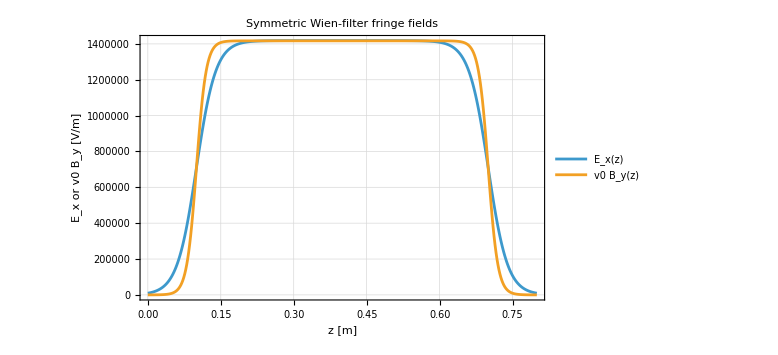

```mathematica
mElectron=9.1093837015*10^-31;
cLight=299792458.;
eCharge=1.602176634*10^-19;

gamma0=1+KE0*eCharge/(mElectron*cLight^2);
beta0=Sqrt[1-1/gamma0^2];
v0=beta0*cLight;

B0=0.006;                  (*Tesla*)
E0=v0*B0;                 (*V/m,Wien condition in uniform region*)

ClearAll[BuildSymmetricWienFields];
Options[BuildSymmetricWienFields]={"InterpolationOrder"->Automatic,"Step"->0.01,"EDirection"->{1,0,0},"BDirection"->{0,1,0},AccuracyGoal->10,PrecisionGoal->10,MaxStepFraction->1/500,MaxIterations->50};

BuildSymmetricWienFields[zMin_,zMax_,zInE_,aE_,aB_,E0_,B0_,v0_,dz_:0.002,OptionsPattern[]]:=Module[{zCen,zOutE,nIntervals,actualDz,zGrid,interpOrder,fringe,makeETable,makeBTable,eFieldTable,bFieldTableInitial,bFieldTableClosed,m=9.1093837015*10^-31,c=299792458.,gamma0,pz0,refParticle,trackOnce,closureX,closureXP,zInBGuess,bScaleGuess,zInBClosed,bScaleClosed,zOutBClosed,sol,refResult,final},zCen=(zMin+zMax)/2;
zOutE=2 zCen-zInE;
interpOrder=OptionValue["InterpolationOrder"]/. Automatic->("InterpolationOrder"/. Options[WienFilterTrack]);
(*Symmetric grid,zCen exactly on grid*)nIntervals=Max[2,2 Ceiling[(zMax-zMin)/(2 dz)]];
actualDz=(zMax-zMin)/nIntervals;
zGrid=N@Subdivide[zMin,zMax,nIntervals];
fringe[z_,zIn_,zOut_,a_]:=1/2*(Tanh[(z-zIn)/a]-Tanh[(z-zOut)/a]);
makeETable[]:=N@Table[{z,E0*fringe[z,zInE,zOutE,aE]},{z,zGrid}];
makeBTable[zInB_?NumericQ,bScale_?NumericQ]:=N@Table[{z,bScale*B0*fringe[z,zInB,2 zCen-zInB,aB]},{z,zGrid}];
eFieldTable=makeETable[];
zInBGuess=zInE;
bScaleGuess=1.0;
bFieldTableInitial=makeBTable[zInBGuess,bScaleGuess];
If[!MatrixQ[eFieldTable,NumericQ],Return[<|"ClosedQ"->False,"Failed"->True,"Reason"->"EFieldTable is not numerical.","EFieldTable"->eFieldTable,"BFieldTable"->bFieldTableInitial|>]];
If[!MatrixQ[bFieldTableInitial,NumericQ],Return[<|"ClosedQ"->False,"Failed"->True,"Reason"->"Initial BFieldTable is not numerical.","EFieldTable"->eFieldTable,"BFieldTable"->bFieldTableInitial|>]];
(*Reference particle from v0*)gamma0=1/Sqrt[1-(v0/c)^2];
pz0=gamma0*m*v0;
refParticle={{0.,0.,zMin,0.,0.,pz0}};
trackOnce[zInB_?NumericQ,bScale_?NumericQ]:=Module[{btab,r,f},btab=makeBTable[zInB,bScale];
If[!MatrixQ[btab,NumericQ],Return[{10^9,10^9}]];
r=Quiet@Check[WienFilterTrack[refParticle,eFieldTable,btab,"Step"->OptionValue["Step"],"ZStart"->zMin,"ZEnd"->zMax,"InterpolationOrder"->interpOrder,"EDirection"->OptionValue["EDirection"],"BDirection"->OptionValue["BDirection"],AccuracyGoal->OptionValue[AccuracyGoal],PrecisionGoal->OptionValue[PrecisionGoal],MaxStepFraction->OptionValue[MaxStepFraction]],$Failed];
If[r===$Failed,Return[{10^9,10^9}]];
f=Last[r["Distributions"]][[1]];
{N[f[[1]]],(*xFinal[m]*)N[f[[4]]/f[[6]]]    (*xpFinal=px/pz*)}];

closureXP[zInB_?NumericQ,bScale_?NumericQ]:=trackOnce[zInB,bScale][[2]];
sol=Quiet@Check[FindRoot[{closureXP[zInBGuess,bScaleVar]==0},{bScaleVar,bScaleGuess},AccuracyGoal->OptionValue[AccuracyGoal],PrecisionGoal->OptionValue[PrecisionGoal],MaxIterations->OptionValue[MaxIterations]],$Failed];
If[sol===$Failed,Return[<|"ClosedQ"->False,"Failed"->True,"Reason"->"FindRoot failed. Returning initial B field.","zMin"->zMin,"zMax"->zMax,"zCen"->zCen,"zInE"->zInE,"zOutE"->zOutE,"zInB"->zInBGuess,"zOutB"->2 zCen-zInBGuess,"BScale"->bScaleGuess,"InterpolationOrder"->interpOrder,"InitialOrbitCheck"->trackOnce[zInBGuess,bScaleGuess],"EFieldTable"->eFieldTable,"BFieldTable"->bFieldTableInitial|>]];
zInBClosed=zInBGuess;
bScaleClosed=bScaleVar/. sol;
zOutBClosed=2 zCen-zInBClosed;
bFieldTableClosed=makeBTable[zInBClosed,bScaleClosed];
refResult=Quiet@Check[WienFilterTrack[refParticle,eFieldTable,bFieldTableClosed,"Step"->OptionValue["Step"],"ZStart"->zMin,"ZEnd"->zMax,"InterpolationOrder"->interpOrder,"EDirection"->OptionValue["EDirection"],"BDirection"->OptionValue["BDirection"],AccuracyGoal->OptionValue[AccuracyGoal],PrecisionGoal->OptionValue[PrecisionGoal],MaxStepFraction->OptionValue[MaxStepFraction]],$Failed];
If[refResult===$Failed,Return[<|"ClosedQ"->False,"Failed"->True,"Reason"->"Final reference tracking failed. Returning closed B table but no final check.","zInB"->zInBClosed,"zOutB"->zOutBClosed,"BScale"->bScaleClosed,"InterpolationOrder"->interpOrder,"EFieldTable"->eFieldTable,"BFieldTable"->bFieldTableClosed|>]];
final=Last[refResult["Distributions"]][[1]];
<|"ClosedQ"->True,"Failed"->False,"zMin"->zMin,"zMax"->zMax,"zCen"->zCen,"RequestedDz"->dz,"ActualDz"->actualDz,"NIntervals"->nIntervals,"InterpolationOrder"->interpOrder,"zInE"->zInE,"zOutE"->zOutE,"aE"->aE,"zInB"->zInBClosed,"zOutB"->zOutBClosed,"aB"->aB,"BScale"->bScaleClosed,"ReferenceOrbitCheck"-><|"xFinal"->final[[1]],"pxFinal"->final[[4]],"pzFinal"->final[[6]],"xpFinal"->final[[4]]/final[[6]]|>,"EFieldTable"->eFieldTable,"BFieldTable"->bFieldTableClosed,"ReferenceResult"->refResult|>];

zMin=0.;
zMax=0.8;

zInE=0.1;
aE=0.04;
aB=0.02;

fields=BuildSymmetricWienFields[zMin,zMax,zInE,aE,aB,E0,B0,v0,0.002,"InterpolationOrder"->("InterpolationOrder"/. Options[WienFilterTrack]),"Step"->0.01,"EDirection"->{1,0,0},"BDirection"->{0,1,0}];


fields["ClosedQ"]
fields["ReferenceOrbitCheck"]
fields["ReferenceOrbitCheck"]["xFinal"]
fields["ReferenceOrbitCheck"]["xpFinal"]


eFieldTable=fields["EFieldTable"];
bFieldTable=fields["BFieldTable"];
ePlotData=eFieldTable;

vBPlotData=Table[{bFieldTable[[i,1]],v0*bFieldTable[[i,2]]},{i,Length[bFieldTable]}];

ListLinePlot[{ePlotData,vBPlotData},Frame->True,Axes->False,FrameLabel->{"z [m]","E_x or v0 B_y [V/m]"},PlotLegends->{"E_x(z)","v0 B_y(z)"},PlotLabel->"Symmetric Wien-filter fringe fields",ImageSize->Large,GridLines->Automatic]
```

#### results

```mathematica
result=WienFilterTrack[particles,eFieldTable,bFieldTable];
zPlanes=result["ZPlanes"];
distributions=result["Distributions"];
```

#### Figures

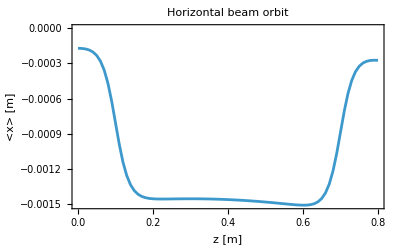

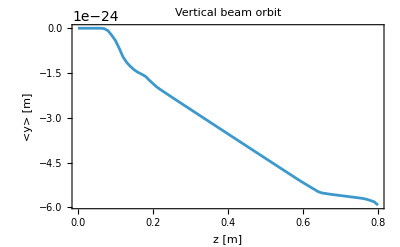

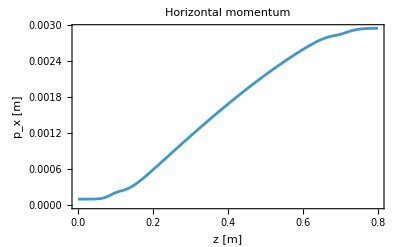

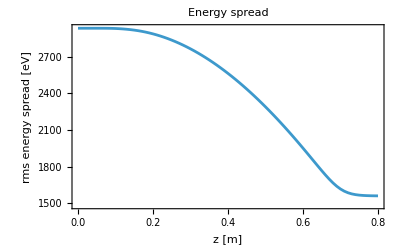

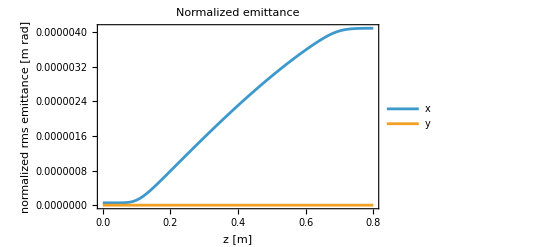

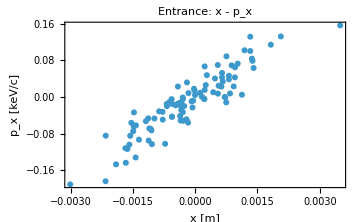
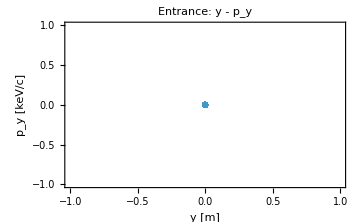
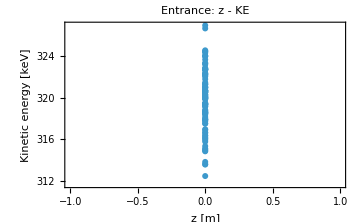

```mathematica
ClearAll[PlotParticlePhaseSpaces,PlotZbeam];


PlotZbeam[result_,eRange_:Automatic]:=Module[{dist,nSteps,nParticles,m=9.1093837015*10^-31,c=299792458.,e=1.602176634*10^-19,keV,data,allKE,range,cf,scaleKE,keColor,curvesZX,curvesZXP,p1,p2},dist=result["Distributions"];
nSteps=Length[dist];
nParticles=Min[Length/@dist];
keV[p_]:=Module[{g},g=Sqrt[1+(p.p)/(m^2*c^2)];
(g-1)*m*c^2/e/1000];
data=Table[{dist[[k,i,3]],(*z[m]*)dist[[k,i,1]],(*x[m]*)dist[[k,i,4]]/dist[[k,i,6]],(*x'=px/pz*)keV[dist[[k,i,4;;6]]]  (*KE[keV]*)},{i,nParticles},{k,nSteps}];
allKE=Flatten[data[[All,All,4]]];
range=eRange/. Automatic->MinMax[allKE];
cf=ColorData["TemperatureMap"];
scaleKE[ke_]:=If[range[[2]]==range[[1]],0.5,Clip[Rescale[ke,range],{0,1}]];
keColor=Function[{ke},cf[scaleKE[ke]]];
curvesZX=Table[Table[{keColor[Mean[data[[i,{k,k+1},4]]]],Thick,Line[data[[i,{k,k+1},{1,2}]]]},{k,nSteps-1}],{i,nParticles}];
curvesZXP=Table[Table[{keColor[Mean[data[[i,{k,k+1},4]]]],Thick,Line[data[[i,{k,k+1},{1,3}]]]},{k,nSteps-1}],{i,nParticles}];
p1=Legended[Graphics[curvesZX,Frame->True,Axes->False,FrameLabel->{"z [m]","x [m]"},PlotLabel->"z - x trajectory colored by kinetic energy",ImageSize->Large,AspectRatio->1/3,PlotRange->All,GridLines->Automatic],BarLegend[{keColor,range},LegendLabel->"KE [keV]"]];
p2=Legended[Graphics[curvesZXP,Frame->True,Axes->False,FrameLabel->{"z [m]","x' = p_x/p_z"},PlotLabel->"z - x' trajectory colored by kinetic energy",ImageSize->Large,AspectRatio->1/3,PlotRange->All,GridLines->Automatic],BarLegend[{keColor,range},LegendLabel->"KE [keV]"]];
{p1,p2}];


Options[PlotParticlePhaseSpaces]={"PointSize"->0.012,"ImageSize"->Large,"PlotLayout"->"Row","PlotLabelPrefix"->""};

PlotParticlePhaseSpaces[particlesIn_,OptionsPattern[]]:=Module[{particles,pointSize,imageSize,layout,prefix,m,c,e,kineticEnergykeV,pSIToKeVoverC,xpxData,ypyData,zkEData,p1,p2,p3},particles=N[particlesIn];
If[!MatrixQ[particles,NumericQ]||Dimensions[particles][[2]]=!=6,Print["Error: input must be an N x 6 particle array: {x,y,z,px,py,pz}."];
Return[$Failed];];
pointSize=OptionValue["PointSize"];
imageSize=OptionValue["ImageSize"];
layout=OptionValue["PlotLayout"];
prefix=OptionValue["PlotLabelPrefix"];
m=9.1093837015*10^-31;
c=299792458.;
e=1.602176634*10^-19;
(*momentum:SI kg m/s->keV/c*)pSIToKeVoverC[pSI_]:=pSI*c/e/1000.;
(*kinetic energy from full relativistic momentum,output in keV*)kineticEnergykeV[pvec_]:=Module[{gamma},gamma=Sqrt[1.+(pvec.pvec)/(m^2*c^2)];
(gamma-1.)*m*c^2/e/1000.];
xpxData=Table[{particles[[i,1]],pSIToKeVoverC[particles[[i,4]]]},{i,Length[particles]}];
ypyData=Table[{particles[[i,2]],pSIToKeVoverC[particles[[i,5]]]},{i,Length[particles]}];
zkEData=Table[{particles[[i,3]],kineticEnergykeV[particles[[i,4;;6]]]},{i,Length[particles]}];
p1=ListPlot[xpxData,Frame->True,Axes->False,FrameLabel->{"x [m]","p_x [keV/c]"},PlotLabel->prefix<>"x - p_x",PlotStyle->PointSize[pointSize],ImageSize->Medium];
p2=ListPlot[ypyData,Frame->True,Axes->False,FrameLabel->{"y [m]","p_y [keV/c]"},PlotLabel->prefix<>"y - p_y",PlotStyle->PointSize[pointSize],ImageSize->Medium];
p3=ListPlot[zkEData,Frame->True,Axes->False,FrameLabel->{"z [m]","Kinetic energy [keV]"},PlotLabel->prefix<>"z - KE",PlotStyle->PointSize[pointSize],ImageSize->Medium];
{p1,p2,p3}];

bp=result["BeamParameters"];

ListLinePlot[{#["z"],#["XOrbit"]}&/@bp,Frame->True,FrameLabel->{"z [m]","<x> [m]"},PlotLabel->"Horizontal beam orbit"]
ListLinePlot[{#["z"],#["YOrbit"]}&/@bp,Frame->True,
FrameLabel->{"z [m]","<y> [m]"},PlotLabel->"Vertical beam orbit"]
ListLinePlot[{#["z"],#["SigmaXp"]}&/@bp,Frame->True,
FrameLabel->{"z [m]","p_x [m]"},PlotLabel->"Horizontal momentum"]
ListLinePlot[{#["z"],#["SigmaKineticEnergy_eV"]}&/@bp,Frame->True,FrameLabel->{"z [m]","rms energy spread [eV]"},PlotLabel->"Energy spread"]
ListLinePlot[{({#["z"],#["EmitXNorm_mrad"]}&/@bp),({#["z"],#["EmitYNorm_mrad"]}&/@bp)},Frame->True,FrameLabel->{"z [m]","normalized rms emittance [m rad]"},PlotLegends->{"x","y"},PlotLabel->"Normalized emittance"]

PlotParticlePhaseSpaces[particles,"PlotLabelPrefix"->"Entrance: "]
(*
k=20;
PlotParticlePhaseSpaces[result["Distributions"][[k]],"PlotLabelPrefix"->"z = "<>ToString[NumberForm[result["ZPlanes"][[k]],{5,3}]]<>" m: "]
*)
PlotParticlePhaseSpaces[Last[result["Distributions"]],"PlotLabelPrefix"->"Exit: "]
PlotZbeam[result]
```